TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

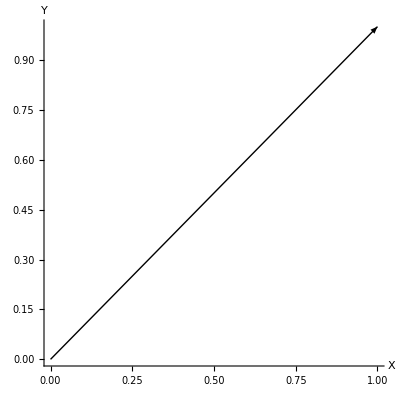

```mathematica
(*Application of matrices and matrix rotations in video games*)
(*Rahul Mitra*)
(*Physics - 300*)
(*Instructor - Barbara Walden*)

(*Rotation of a 2D vector*)
vector1 = {1,1};(*Vector with components <1,1>*)
rotationmatrix = RotationTransform[a](*Rotation transform is a really neat mathematica feature that gives you the rotation matrix for any particular angle*)
Graphics[{Arrow[{{0,0},vector1}]},Axes->True,AxesLabel->{"X","Y"}](*Plot the vector in 2 Dimensional space*)
```

```mathematica
(*Now let's we want to rotate vector1 by some user inputted angle in the counterclockwise direction*)
(*We use matrices!*)
```

```mathematica
angle = Input["Enter angle in radians"];(*User inputted rotation angle*)
RotationMat = RotationMatrix[angle];(*We find the rotation matrix*)
RotationMat//MatrixForm
```

((√3)/2 | -1/2
1/2 | (√3)/2)

```mathematica
NewVector = RotationMat.vector1;(*Multiply the current vector by the rotation matrix to get the translated vector*)
NewVector //MatrixForm
```

(-1/2+(√3)/2
1/2+(√3)/2)

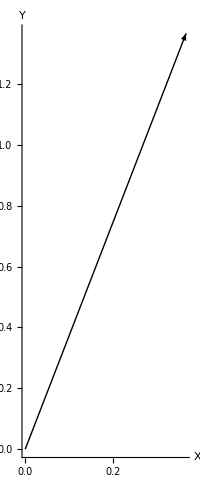

```mathematica
Graphics[{Arrow[{{0,0},NewVector}]},Axes->True,AxesLabel->{"X","Y"}](*Plot the new vector in 2 Dimensional space*)
```

```mathematica
(*Now we go to the 3-Dimensional case*)
(*3 arbitrary vectors - vec1, vec2 and vec3*)
```

```mathematica
vec1 = {1,2,3};
vec2 = {4,5,6};
vec3 = {5,6,7};
```

```mathematica
Graphics3D[Arrow[{{0,0,0},vec1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium](*Plotting vec1*)
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{{0,0,0},vec2}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium](*Plotting vec2*)
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{{0,0,0},vec3}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium](*Plotting vec3*)
```

-Graphics3D-

```mathematica
data={vec1,vec2,vec3};

Graphics3D[Arrow[{{0,0,0},#}]&/@data,Axes -> True,AxesLabel->{"X","Y","Z"}](*All three vector plotted together*)
```

-Graphics3D-

```mathematica
(*We can plot them together*)
```

```mathematica
(*Now say we want to rotate vec1 around the z axis by some user inputted angle*)
angleZ = Input["Enter angle in radians"];
rotation3D = RotationTransform[a,{0,0,1}](*This gives the rotation in matrix in 3-Dimensions about the Z axis*)
Rotationz = RotationMatrix[angleZ, {0,0,1}];
Rotationz//MatrixForm
```

TransformationFunction[(Cos[a] | -Sin[a] | 0 | 0
Sin[a] | Cos[a] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
RotatedVec1 = Rotationz.vec1;
RotatedVec1//MatrixForm
```

(-1
-2
3)

```mathematica
Graphics3D[Arrow[{{0,0,0},RotatedVec1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large](*This gives rotated vec1 about the Z-axis by some user inputted angle*)
```

-Graphics3D-

```mathematica
(*In real game development, however, rotations are not that easy. You usually don't rotate about a fixed axes but need one vector to rotate in the direction of another vector*)
vec = Input["Enter the direction you want to rotate vec2 in"];
vec2 = {4,5,6};
rotatemat2 = RotationMatrix[{vec2,vec}];
rotatemat2//MatrixForm
```

(1/462 (77+80 √22) | 1/462 (-154+23 √22) | 1/462 (77-34 √22)
1/462 (-154+41 √22) | 2/231 (77+8 √22) | 1/462 (-154+23 √22)
1/462 (77+2 √22) | 1/462 (-154+41 √22) | 1/462 (77+80 √22))

```mathematica
(*Let's plot the rotated vec2*)
```

```mathematica
RotatedVec2 = rotatemat2.vec2;
RotatedVec2//MatrixForm
```

(1/77 (77-34 √22)+5/462 (-154+23 √22)+2/231 (77+80 √22)
10/231 (77+8 √22)+1/77 (-154+23 √22)+2/231 (-154+41 √22)
2/231 (77+2 √22)+5/462 (-154+41 √22)+1/77 (77+80 √22))

```mathematica
Graphics3D[Arrow[{{0,0,0},RotatedVec2}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large](*Plotting the new matrix*)
```

-Graphics3D-

```mathematica
(*Another example of rotating one vector in the direction of another*)
```

```mathematica
rotate1 = RotationMatrix[{vec1,vec2}];(*gives the matrix that rotates vec1 in the direction of vec2*)
rotate1 //MatrixForm
rotated1 = rotate1.vec1;(*Evaluating the new rotated matrix*)
Graphics3D[Arrow[{{0,0,0},rotated1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large](*Plotting the new matrix*)
```

(1/462 (77+80 √22) | 1/462 (-154+41 √22) | 1/462 (77+2 √22)
1/462 (-154+23 √22) | 2/231 (77+8 √22) | 1/462 (-154+41 √22)
1/462 (77-34 √22) | 1/462 (-154+23 √22) | 1/462 (77+80 √22))

-Graphics3D-

```mathematica
(*So we have finally got all our information to actually understand graphics*)
(*First let's talk about a bad axis to rotate around*)
(*If my game had a monochromatic cylinder, rotating about the Z axis would be a terrible idea!*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cylinder[],a Degree,{0,0,1}]],{a,0,360}](*Here's an example of choosing a bad axis to rotated around - in this case Z*)
```

```mathematica
(*Here's the same cylinder, but now rotating around the X-axis*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cylinder[],a Degree,{1,0,0}]],{a,0,360}]
```

```mathematica
(*Whilst rotating a cube, choosing the axis of rotating becomes a lot less important*)
```

```mathematica
(*This cube rotates 360 degress about the z-axis*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cuboid[],a Degree,{0,0,1}]],{a,0,360}]
```

```mathematica
(*This rotates the cube about the Y-axis*)
Manipulate[Graphics3D[Rotate[Cuboid[],a Degree,{0,1,0}]],{a,0,360}]
```

```mathematica
(*Or just as simply rotated the cube around the X-axis*)
```

```mathematica
Manipulate[Graphics3D[Rotate[Cuboid[],a Degree,{1,0,0}]],{a,0,360}]
```

```mathematica
(*We could do the same with vectors which is perhaps a little more relevant to graphics design*)
```

```mathematica
Manipulate[Graphics[{Arrow[{{0,0},RotationMatrix[a].{1,1}}]},Axes->True],{a,0,2*Pi}](*Rotating a 2-D vector all around the XY plane*)
```

```mathematica
(*We could even extrapolate this to the 3-Dimensional vector case*)
```

```mathematica
(*This rotates a vector around the Z axis for a full 360 degree cycle. It's my favorite graphic in this whole project - it's simple, yet so descriptive!*)
```

```mathematica
Manipulate[Graphics3D[Arrow[{{0,0,0},RotationMatrix[a,{0,0,1}].{1,2,3}}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium],{a,0,2*Pi}]
```

```mathematica
(*Again we can extrapolate the single vector to be rotated around the X axis and the Y axis*)
(*Here is the single vector rotated around the X axis*)
```

```mathematica
Manipulate[Graphics3D[Arrow[{{0,0,0},RotationMatrix[a,{1,0,0}].{1,2,3}}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium],{a,0,2*Pi}]
```

```mathematica
(*And here it is rotated around the Y axis*)
Manipulate[Graphics3D[Arrow[{{0,0,0},RotationMatrix[a,{0,1,0}].{1,2,3}}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium],{a,0,2*Pi}]
```

```mathematica
(*All in all, matrices are very powerful tools to visualize object animations and rotations in video games. When vectors are represeted as matrices, one can easily calculate the rotation matrices for any particular angle and mathematica is an ideal tool to visualize those rotaions.Hopefully through this project, I've been able to give the class a better understanding of the applications of vectors,matrices and rotations in video game engines.*)
```